# Peters & Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 No. 1(1 July 1963) 435.

See R. O. Hansen, “Post-Newtonian Gravitational Radiation from Point Masses in a Hyperbolic Kepler Orbit,” Phys. Rev. 5 no. 4 (15 Feb 1972) 1021.  He uses the 2.5 order post-Newtonian to avoid averaging when finding the power radiated.  Adds another term to Peters and Mathews.

Instantaneous Power radiated, not yet averaged. Eqn (15).

```mathematica
Pow = 8/15 G^4/c^5(Subscript[m, 1]^2 Subscript[m, 2]^2(Subscript[m, 1]+Subscript[m, 2]))/(a^5(1-e^2)^5)(1-e Cos[ψ])^4( 12(1+e Cos[ψ])^2+e^2 Sin[ψ]^2)
```

(8 G^4 (1-e Cos[ψ])^4 (12 (1+e Cos[ψ])^2+e^2 Sin[ψ]^2) m_1^2 m_2^2 (m_1+m_2))/(15 a^5 c^5 (1-e^2)^5)

```mathematica
AngPart = ((1-e Cos[ψ])^4( 12(1+e Cos[ψ])^2+e^2 Sin[ψ]^2))/((1-e^2)^5)
```

((1-e Cos[ψ])^4 (12 (1+e Cos[ψ])^2+e^2 Sin[ψ]^2))/((1-e^2)^5)

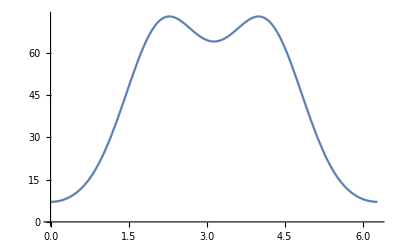

```mathematica
Plot[AngPart /.{e->0.5},{ψ,0,2 π}]
```

```mathematica
AvgPart=1/(2π)∫_0^(2π) AngPart ⅆψ
```

-(192-88 e^2-60 e^4+61 e^6)/(16 (-1+e^2)^5)

```mathematica
AvgPart /.{e->0.5}
```

44.037

```mathematica
AvgPart//FullSimplify
```

(-192+88 e^2+60 e^4-61 e^6)/(16 (-1+e^2)^5)

```mathematica
numer=AvgPart//Numerator
```

-192+88 e^2+60 e^4-61 e^6

```mathematica
numer/(1-e^2)//Simplify[#,0≤e<1]&
```

(192-88 e^2-60 e^4+61 e^6)/(-1+e^2)

```mathematica
numer // Factor
```

-192+88 e^2+60 e^4-61 e^6

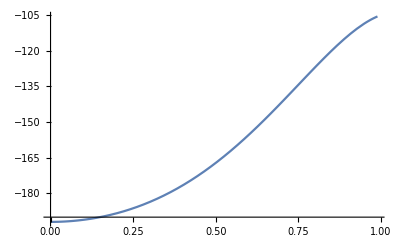

```mathematica
Plot[numer,{e,0,0.99}]
```

```mathematica
eqn16=1/((1-e^2)^(7/2))(1+73/24 e^2+37/96 e^4)
```

(1+(73 e^2)/24+(37 e^4)/96)/((1-e^2)^(7/2))

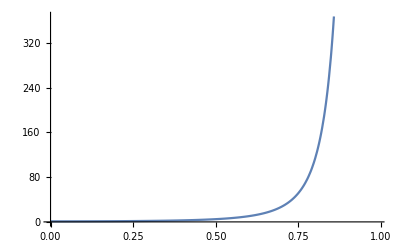

```mathematica
Plot[eqn16,{e,0, 0.99}]
```

Maybe Eqn (15) is wrong!  Check it with the Eqns (12)-(14) applied to Eqn (6).

```mathematica
Qttt[1,1]=β (1+e Cos[ψ])^2(2 Sin[2ψ]+3e Sin[ψ] Cos[ψ]^2);
Qttt[2,2]=-β(1+e Cos[ψ])^2(2 Sin[2ψ]+e Sin[ψ](1+3e Cos[ψ]^2) );
Qttt[1,2]=-β (1+e Cos[ψ])^2(2 Cos[2ψ]-e Cos[ψ](1-3e Cos[ψ]^2) );
Qttt[2,1]=-β (1+e Cos[ψ])^2(2 Cos[2ψ]-e Cos[ψ](1-3e Cos[ψ]^2) );
```

```mathematica
Peqn6 = G/(5 c^5)Sum[Qttt[i,j]Qttt[i,j]-1/3 Qttt[i,i]Qttt[j,j],{i,1,2},{j,1,2}]//Simplify//FunctionExpand[#,0≤e<1]&
```

1/(15 c^5)2 G β^2 (1+e Cos[ψ])^4 (3 (e Cos[ψ]-3 e^2 Cos[ψ]^3-2 Cos[2 ψ])^2+Cos[ψ]^2 (4+3 e Cos[ψ])^2 Sin[ψ]^2+Cos[ψ] (4+3 e Cos[ψ]) Sin[ψ] (e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])+(e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])^2)

```mathematica
exprAng=(3 (e Cos[ψ] (-1+3 e Cos[ψ]^2)+2 Cos[2 ψ])^2+Cos[ψ]^2 (4+3 e Cos[ψ])^2 Sin[ψ]^2+Cos[ψ] (4+3 e Cos[ψ]) Sin[ψ] (e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])+(e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])^2)
```

3 (e Cos[ψ] (-1+3 e Cos[ψ]^2)+2 Cos[2 ψ])^2+Cos[ψ]^2 (4+3 e Cos[ψ])^2 Sin[ψ]^2+Cos[ψ] (4+3 e Cos[ψ]) Sin[ψ] (e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])+(e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])^2

```mathematica
exprAng//TrigExpand//Factor
```

1/32 (384+94 e^2-174 e^3+288 e^4+48 e Cos[ψ]+720 e^2 Cos[ψ]+41 e^2 Cos[ψ]^2-279 e^3 Cos[ψ]^2+414 e^4 Cos[ψ]^2-360 e Cos[ψ]^3+360 e^2 Cos[ψ]^3-30 e^2 Cos[ψ]^4-114 e^3 Cos[ψ]^4+144 e^4 Cos[ψ]^4-72 e Cos[ψ]^5+72 e^2 Cos[ψ]^5-9 e^2 Cos[ψ]^6-9 e^3 Cos[ψ]^6+18 e^4 Cos[ψ]^6-41 e^2 Sin[ψ]^2+279 e^3 Sin[ψ]^2-414 e^4 Sin[ψ]^2+1080 e Cos[ψ] Sin[ψ]^2-1080 e^2 Cos[ψ] Sin[ψ]^2+180 e^2 Cos[ψ]^2 Sin[ψ]^2+684 e^3 Cos[ψ]^2 Sin[ψ]^2-864 e^4 Cos[ψ]^2 Sin[ψ]^2+720 e Cos[ψ]^3 Sin[ψ]^2-720 e^2 Cos[ψ]^3 Sin[ψ]^2+135 e^2 Cos[ψ]^4 Sin[ψ]^2+135 e^3 Cos[ψ]^4 Sin[ψ]^2-270 e^4 Cos[ψ]^4 Sin[ψ]^2-30 e^2 Sin[ψ]^4-114 e^3 Sin[ψ]^4+144 e^4 Sin[ψ]^4-360 e Cos[ψ] Sin[ψ]^4+360 e^2 Cos[ψ] Sin[ψ]^4-135 e^2 Cos[ψ]^2 Sin[ψ]^4-135 e^3 Cos[ψ]^2 Sin[ψ]^4+270 e^4 Cos[ψ]^2 Sin[ψ]^4+9 e^2 Sin[ψ]^6+9 e^3 Sin[ψ]^6-18 e^4 Sin[ψ]^6)

```mathematica
Sum[mm[i,j]mm[i,j]-1/3 mm[i,i]mm[j,j],{i,1,2},{j,1,2}]
```

2/3 mm[1,1]^2+mm[1,2]^2+mm[2,1]^2-2/3 mm[1,1] mm[2,2]+2/3 mm[2,2]^2

```mathematica
Peqn6con = Peqn6/.{β->√((4 G^3 Subscript[m, 1]^2 Subscript[m, 2]^2(Subscript[m, 1]+Subscript[m, 2]))/(a^5(1-e^2)^5))}/.{G->1,c->1,Subscript[m, 1]->1,Subscript[m, 2]->1,a->1}
```

1/(15 (1-e^2)^5)16 (1+e Cos[ψ])^4 (3 (e Cos[ψ]-3 e^2 Cos[ψ]^3-2 Cos[2 ψ])^2+Cos[ψ]^2 (4+3 e Cos[ψ])^2 Sin[ψ]^2+Cos[ψ] (4+3 e Cos[ψ]) Sin[ψ] (e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])+(e (1+3 e Cos[ψ]^2) Sin[ψ]+2 Sin[2 ψ])^2)

```mathematica
Powcon=Pow/.{G->1,c->1,Subscript[m, 1]->1,Subscript[m, 2]->1,a->1}
```

(16 (1-e Cos[ψ])^4 (12 (1+e Cos[ψ])^2+e^2 Sin[ψ]^2))/(15 (1-e^2)^5)

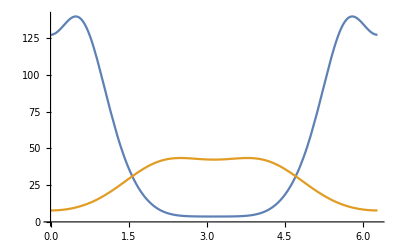

```mathematica
Plot[{Peqn6con/.{e->0.4},Powcon/.{e->0.4}},{ψ,0,2π}]
```

## Keplerian motion, use P&M geometry

Let the motion be in the x-y plane, origin at the center of mass, and m_1 at d_1 away at angle ψ from the x-axis, while m_2 is d_2 away at the opposite side.

```mathematica
x[1]= Subscript[m, 2]/(Subscript[m, 1]+Subscript[m, 2])d Cos[ψ]; (* for mass Subscript[m, 1] *)
y[1]=Subscript[m, 2]/(Subscript[m, 1]+Subscript[m, 2])d Sin[ψ];
x[2]= -Subscript[m, 1]/(Subscript[m, 1]+Subscript[m, 2])d Cos[ψ];(* for mass Subscript[m, 2] *)
y[2]=-Subscript[m, 1]/(Subscript[m, 1]+Subscript[m, 2])d Sin[ψ];
d=a(1-e^2)/(1+e Cos[ψ]);
```

```mathematica
x[1]
```

(a (1-e^2) Cos[ψ] m_2)/((1+e Cos[ψ]) (m_1+m_2))

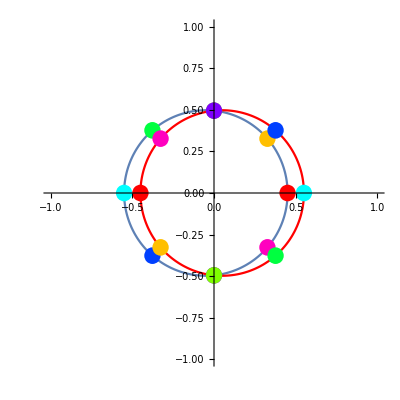

```mathematica
myconst={Subscript[m, 1]->1,Subscript[m, 2]->1,e->0.1,a->1.0};
ballrad=0.05;
aplot[1]=ParametricPlot[ {x[1],y[1]}/.myconst,{ψ,0,2π}, PlotRange->{{-1,1},{-1,1}},DisplayFunction->Identity];
aplot[2]=ParametricPlot[ {x[2],y[2]}/.myconst,{ψ,0,2π}, PlotStyle->{RGBColor[{1,0,0}]},DisplayFunction->Identity];
agraphic[3]=Table[{Hue[i/8.],Ball[{x[1],y[1]}/.myconst/.ψ->i 2 π/8,ballrad]},{i,1,8}];
(*aplot[3]=ListPlot[adata[3], DisplayFunction->Identity];*)
(*adata[4]=Table[{x[2],y[2]}/.myconst/.ψ->i 2 π/8,{i,1,8}];*)
agraphic[4]=Table[{Hue[i/8.],Ball[{x[2],y[2]}/.myconst/.ψ->i 2 π/8,ballrad]},{i,1,8}];
(*aplot[4]=ListPlot[adata[4], DisplayFunction->Identity, PlotRange->All];*)
Show[{aplot[1],aplot[2], Graphics[{agraphic[3],agraphic[4]}] },DisplayFunction->$DisplayFunction]
```

```mathematica
{{x[1],y[1]},{x[2],y[2]}}
```

{{(a (1-e^2) Cos[ψ] m_2)/((1+e Cos[ψ]) (m_1+m_2)),(a (1-e^2) Sin[ψ] m_2)/((1+e Cos[ψ]) (m_1+m_2))},{-(a (1-e^2) Cos[ψ] m_1)/((1+e Cos[ψ]) (m_1+m_2)),-(a (1-e^2) Sin[ψ] m_1)/((1+e Cos[ψ]) (m_1+m_2))}}

Quadrupole is Q_ij=∑_α m_α x_αi x_αj , P&M eqn (4).

```mathematica
Q[1,1]=∑_(k=1)^2 Subscript[m, k] x[k]x[k] // FullSimplify
```

(a^2 (-1+e^2)^2 Cos[ψ]^2 m_1 m_2)/((1+e Cos[ψ])^2 (m_1+m_2))

```mathematica
Q[2,2]=∑_(k=1)^2 Subscript[m, k] y[k]y[k] // FullSimplify
```

(a^2 (-1+e^2)^2 Sin[ψ]^2 m_1 m_2)/((1+e Cos[ψ])^2 (m_1+m_2))

```mathematica
Q[1,2]=∑_(k=1)^2 Subscript[m, k] x[k]y[k] // FullSimplify
```

(a^2 (-1+e^2)^2 Sin[2 ψ] m_1 m_2)/(2 (1+e Cos[ψ])^2 (m_1+m_2))

```mathematica
Q[2,1]=∑_(k=1)^2 Subscript[m, k] y[k]x[k] // FullSimplify
```

(a^2 (-1+e^2)^2 Sin[2 ψ] m_1 m_2)/(2 (1+e Cos[ψ])^2 (m_1+m_2))

```mathematica
Q[1,2]==Q[2,1]
```

True

Work on the three time derivatives.

```mathematica
D[Q[1,1]/.ψ->Ψ[t],t]//FullSimplify
```

-(a^2 (-1+e^2)^2 Sin[2 Ψ[t]] m_1 m_2 Ψ'[t])/((1+e Cos[Ψ[t]])^3 (m_1+m_2))

```mathematica
D[d/.ψ->Ψ[t],t]
```

(a e (1-e^2) Sin[Ψ[t]] Ψ'[t])/(1+e Cos[Ψ[t]])^2